```mathematica
<<MaTeX`
```

Get::noopen: Cannot open MaTeX`.

$Failed

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

```mathematica
(*Converts n to a binary string of length l*)
toBin[n_,l_]:= Join[ConstantArray[0,l-Length[IntegerDigits[n,2]]],IntegerDigits[n,2]]
```

```mathematica
(*The ordering of the game. The first entry has to be a total order*)
ordering = {t>r>p>s};
```

```mathematica
(*Normalize by setting the outside parameters to 1 and 0.*)
outside = {First[ordering[[1]]/.{Greater ->List}],Last[ordering[[1]]/.{Greater ->List}]};
values = {outside[[1]]==1,outside[[2]]==0};
inside = DeleteCases[ordering[[1]] /.{Greater->List},Alternatives @@ outside];
changes = values/.{Equal->Rule};
restrictions= ordering/.changes;

(*Drawing restrictions*)
drestrictions = Flatten[{ordering,0<d<1}];

(*All restrictions*)
restrictions = Flatten[{drestrictions,values}];
```

```mathematica
restrictions
```

{t>r>p>s,0<d<1,t==1,s==0}

```mathematica
Q100
```

Q100

0 | {0,0} | {{0→0,True}}
1 | {0,1} | {{1→0,s+d t<p+d s},{1→2,s+d t>p+d s}}
2 | {1,0} | {{2→0,r+d r<d p+t},{2→2,(1+d) r>d p+t}}
3 | {1,1} | {{3→0,True}}

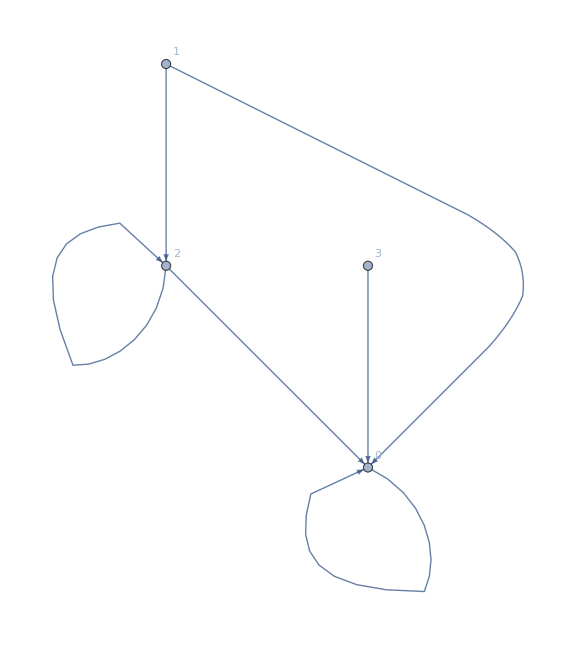

4

```mathematica
result[i_, strats_]:=
Module[{input = i, str = strats},
output = {};
transpoints = {};
(*Check every strat to see if it is a best-response*)
Do[{
strat = str[[j]];
(*Get an ordering of the Q-values based on the strategy-pair*)
assumptions = Flatten[{
               If[strat[[1]]==0, Q100>Q101, Q100<Q101],
               If[strat[[2]]==0, Q110>Q111, Q110<Q111],
               If[input[[1]]==0, Q200>Q201, Q200<Q201],
               If[input[[2]]==0, Q210>Q211, Q210<Q211],
               drestrictions}];

(*Solve the Bellman equations*)
Assuming[assumptions,
{q1 = Simplify[Boole[Q200>Q201] (p+d*Q100*Boole[Q100>Q101]+d*Q101*Boole[Q100<Q101])+
                        Boole[Q200<Q201] (t+d*Q110*Boole[Q110>Q111]+d*Q111*Boole[Q110<Q111])],
q2=  Simplify[Boole[Q200>Q201] (s+d*Q110*Boole[Q110>Q111]+d*Q111*Boole[Q110<Q111])+
                        Boole[Q200<Q201] (r+d*Q100*Boole[Q100>Q101]+d*Q101*Boole[Q100<Q101])],
q3=  Simplify[Boole[Q210>Q211] (p+d*Q100*Boole[Q100>Q101]+d*Q101*Boole[Q100<Q101])+
                        Boole[Q210<Q211] (t+d*Q110*Boole[Q110>Q111]+d*Q111*Boole[Q110<Q111])],
q4=  Simplify[Boole[Q210>Q211] (s+d*Q110*Boole[Q110>Q111]+d*Q111*Boole[Q110<Q111])+
                        Boole[Q210<Q211] (r+d*Q110*Boole[Q110>Q111]+d*Q111*Boole[Q110<Q111])]
}];
sol1=Solve[{q1==Q100, q2==Q101, q3==Q110, q4==Q111},{Q100, Q101, Q110, Q111}];

(*Check when strat is best-response*)
formula = Simplify[Assuming[assumptions,
 Simplify[Reduce[
  If[strat[[1]]==0,Simplify[sol1[[1]][[1]][[2]] > sol1[[1]][[2]][[2]]], Simplify[sol1[[1]][[1]][[2]] < sol1[[1]][[2]][[2]]]] && 
If[strat[[2]]==0,Simplify[sol1[[1]][[3]][[2]] > sol1[[1]][[4]][[2]]], Simplify[sol1[[1]][[3]][[2]] < sol1[[1]][[4]][[2]]]] ,d,Reals]]]];
(*If the strat can be a best-response, add the strategy and the region to the output*)
If[(formula === False)==False , AppendTo[output,{FromDigits[i,2]->j-1,Simplify[formula]}]];
},{j,1,4}];
output
];

(*All binary strategies*)
strats = Table[ Join[ConstantArray[0,2-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]],{i,0,3}];

(*All best-responses*)
transitions = Table[result[strats[[i]],strats],{i,1,4}];

(*Grid of strategies and best-responses*)
grid = Table[{FromDigits[strats[[i]],2], strats[[i]],transitions[[i]]},{i,1,4}];
Grid[grid,Frame->All]

(*Draw a graph with the best-responses*)
edges = Flatten[Table[Table[transitions[[i]][[j]][[1]],{j,1,Length[transitions[[i]]]}],{i,1,Length[transitions]}]];
labels = Flatten[Table[Table[transitions[[i]][[j]][[1]] -> transitions[[i]][[j]][[2]],{j,1,Length[transitions[[i]]]}],{i,1,Length[transitions]}]];
GraphPlot[edges, VertexLabels->Automatic,  DirectedEdges->True, ImageSize->Large]

(*Count the amount of possible graphs*)
Times @@ Table[Length[transitions[[i]]],{i,1,4}]
```

```mathematica
sol1
```

{{Q100→-(d r+t-d t)/(-1+d),Q101→-r/(-1+d),Q110→-(d r+t-d t)/(-1+d),Q111→-r/(-1+d)}}

```mathematica
transitions
```

{{{0→0,True}},{{1→0,s+d t<p+d s},{1→2,s+d t>p+d s}},{{2→0,(1+d) r<d p+t},{2→2,(1+d) r>d p+t}},{{3→0,True}}}

```mathematica
asynchronousBRtransitions = {{}, {}, {}, {}};
Do[sourcestrat=strats[[k]];
Do[targetstrat=strats[[transitions[[k]][[j]][[1]][[2]]+1]];If[sourcestrat[[1]]!= targetstrat[[1]], AppendTo[asynchronousBRtransitions[[k]], {{k-1->Position[strats, {targetstrat[[1]], sourcestrat[[2]]}][[1]][[1]]-1},transitions[[k]][[j]][[2]] }]];If[sourcestrat[[2]]!= targetstrat[[2]], AppendTo[asynchronousBRtransitions[[k]], {{k-1->Position[strats, {sourcestrat[[1]], targetstrat[[2]]}][[1]][[1]]-1}, transitions[[k]][[j]][[2]]}]];
If[sourcestrat[[1]]!= targetstrat[[1]]&&sourcestrat[[2]]!= targetstrat[[2]], AppendTo[asynchronousBRtransitions[[k]], {{k-1->Position[strats, {targetstrat[[1]], targetstrat[[2]]}][[1]][[1]]-1}, transitions[[k]][[j]][[2]]}]];
If[sourcestrat==targetstrat,  AppendTo[asynchronousBRtransitions[[k]], {{k-1->k-1}, transitions[[k]][[j]][[2]]}]], 
{j, 1, Length[transitions[[k]]]}], {k, 1, Length[transitions]}]
```

```mathematica
asynchronousBRtransitions
```

{{{{0→0},True}},{{{1→0},s+d t<p+d s},{{1→3},s+d t>p+d s},{{1→0},s+d t>p+d s},{{1→2},s+d t>p+d s}},{{{2→0},(1+d) r<d p+t},{{2→2},(1+d) r>d p+t}},{{{3→1},True},{{3→2},True},{{3→0},True}}}

```mathematica
asynchronousBRtransitionssimple={{}, {}, {}, {}};
fixedtransitions={};
Do[Do[transitioncollection={};Do[If[Equal[asynchronousBRtransitions[[i]][[j]][[2]],asynchronousBRtransitions[[i]][[k]][[2]]]&&FreeQ[fixedtransitions,asynchronousBRtransitions[[i]][[k]]], AppendTo[transitioncollection, asynchronousBRtransitions[[i]][[k]][[1]][[1]]];AppendTo[fixedtransitions, asynchronousBRtransitions[[i]][[k]]]], {k, j, Length[asynchronousBRtransitions[[i]]]}];
If[Equal[transitioncollection ,{} ],,AppendTo[asynchronousBRtransitionssimple[[i]], {transitioncollection,asynchronousBRtransitions[[i]][[j]][[2]] }]], {j, 1, Length[asynchronousBRtransitions[[i]]]}], {i, 1, Length[asynchronousBRtransitions]}]
```

```mathematica
transitioncollection
```

{}

```mathematica
asynchronousBRtransitionssimple
```

{{{{0→0},True}},{{{1→0},s+d t<p+d s},{{1→3,1→0,1→2},s+d t>p+d s}},{{{2→0},(1+d) r<d p+t},{{2→2},(1+d) r>d p+t}},{{{3→1,3→2,3→0},True}}}

```mathematica
asynchronousBRtransitionssimple[[2]][[2]][[1]]
```

{1→3,1→0,1→2}

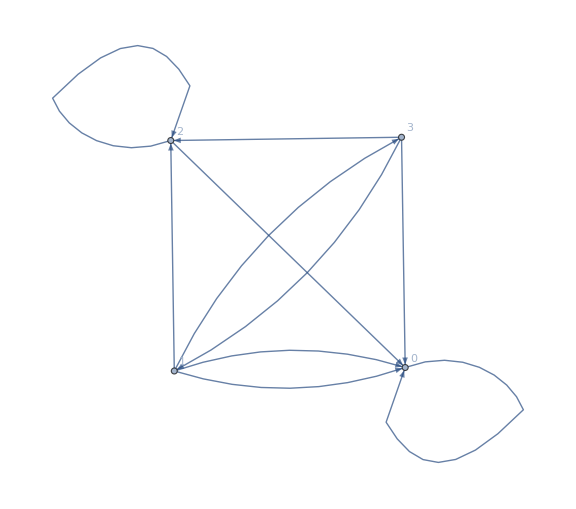

```mathematica
(*Draw a graph with the best-responses*)
edges = Flatten[Table[Table[asynchronousBRtransitionssimple[[i]][[j]][[1]],{j,1,Length[asynchronousBRtransitionssimple[[i]]]}],{i,1,Length[asynchronousBRtransitionssimple]}]];
labels = Flatten[Table[Table[asynchronousBRtransitionssimple[[i]][[j]][[1]] -> asynchronousBRtransitionssimple[[i]][[j]][[2]],{j,1,Length[asynchronousBRtransitionssimple[[i]]]}],{i,1,Length[asynchronousBRtransitionssimple]}]];
GraphPlot[edges, VertexLabels->Automatic,  DirectedEdges->True, ImageSize->Large]
```

```mathematica
(*Find the actual possible graphs by adding a restriction one at the time if it does not yield an empty region*)
(*Here will will get all graphs and their regions*)
(*We will initialise with the transitions from 0 and their regions*)
possible = Table[{asynchronousBRtransitionssimple[[1]][[j]][[1]],asynchronousBRtransitionssimple[[1]][[j]][[2]]},{j,1,Length[asynchronousBRtransitionssimple[[1]]]}];

Do[
(*Updated possible after adding the next round of transitions*)
next = {};
Do[
Do[
(*Add a new transition to possible[[k]]*)
function = Assuming[drestrictions,FullSimplify[And[possible[[k]][[2]],asynchronousBRtransitionssimple[[i]][[j]][[2]]]]];
(*If the new region is non empty, add possible[[k]] with the new transition to next*)
If[(function===False)==False,
next = AppendTo[next,{Flatten[{possible[[k]][[1]],asynchronousBRtransitionssimple[[i]][[j]][[1]]}],Assuming[drestrictions,FullSimplify[And[possible[[k]][[2]],function]]]}];
];
,{k,1,Length[possible]}];
,{j,1,Length[asynchronousBRtransitionssimple[[i]]]}];
possible = next;
,{i,2,4}];
```

```mathematica
(*Add the restrictions*)
Graphs = Table[{possible[[i]][[1]],FullSimplify[possible[[i]][[2]]&&( And @@ drestrictions)]},{i,1,Length[possible]}];
(*Delete regions which will now become empty*)
Graphs = DeleteCases[Graphs,{_,False}];
```

```mathematica
Grid[Table[{i,Graphs[[i]][[1]],Graphs[[i]][[2]]},{i,1,Length[Graphs]}], Frame->All]

edgeslist = Graphs[[All,1]];
todraw = Graphs[[All,2]];
```

1 | {0→0,1→0,2→0,3→1,3→2,3→0} | r+d r<d p+t&&s+d t<p+d s&&t>r>p>s&&0<d<1
2 | {0→0,1→3,1→0,1→2,2→0,3→1,3→2,3→0} | r+d r<d p+t&&s+d t>p+d s&&t>r>p>s&&0<d<1
3 | {0→0,1→0,2→2,3→1,3→2,3→0} | s+d t<p+d s&&(1+d) r>d p+t&&t>r>p>s&&0<d<1
4 | {0→0,1→3,1→0,1→2,2→2,3→1,3→2,3→0} | r+d r>d p+t&&s+d t>p+d s&&t>r>p>s&&0<d<1

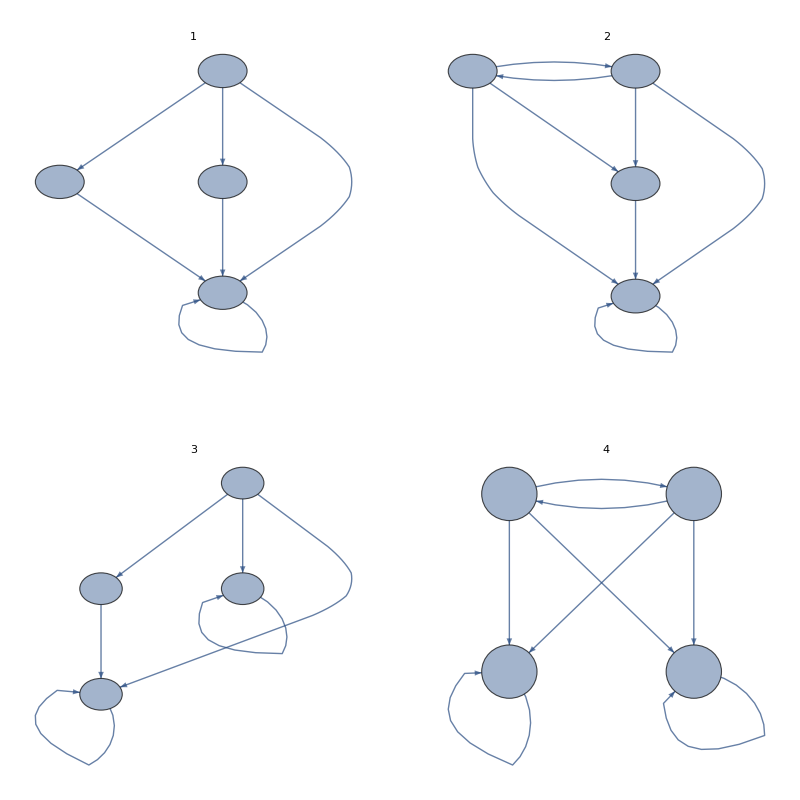

```mathematica
(*Make a grid with the different graphs (as square as possible)*)
grid = ArrayReshape[Table[Graphics[GraphPlot[edgeslist[[i]], VertexLabels->Placed[Automatic,Center],VertexSize->.3,  DirectedEdges->True,PlotLabel->i,PlotStyle->Thick, GraphLayout->"LayeredDigraphEmbedding"]],{i,1,Length[edgeslist]}],{Ceiling[Sqrt[Length[Graphs]]],Ceiling[Sqrt[Length[Graphs]]]}];

(*Convert the zeroes on the empty spaces in the grid to empty graphics*)
Do[Do[If[grid[[i]][[j]]==0, grid[[i]][[j]] = Graphics[{}]],{j,1,Length[grid[[i]]]}],{i,1,Length[grid]}]

(*Delete the empty rows*)
Do[If[grid[[i]] == ConstantArray[Graphics[{}],Length[grid[[i]]]],grid = grid[[1;;i-1]]; Break[]],{i,1,Length[grid]}]

(*Draw the grid*)
GraphicsGrid[grid,Frame->All,ImageSize->Full]
```